# Lagaris Problem 2: 1st-Order Linear ODE IVP

Solving the ODE in Mathematica:

```mathematica
de=ψ'[x]+ψ[x]/5 == ⅇ^(-x/5)Cos[x]
```

ψ[x]/5+ψ'[x]==ⅇ^(-x/5) Cos[x]

```mathematica
generalSolution=FullSimplify[DSolve[de,ψ[x],x]]
```

{{ψ[x]→ⅇ^(-x/5) (C[1]+Sin[x])}}

```mathematica
particularSolution=FullSimplify[DSolve[{de,ψ[0]==0},ψ[x],x]]
```

{{ψ[x]→ⅇ^(-x/5) Sin[x]}}

```mathematica
ψa[x_]:=ψ[x]/.particularSolution[[1]]
```

Compute the derivative of the solution.

```mathematica
FullSimplify[D[ψa[x],x]]
```

1/5 ⅇ^(-x/5) (5 Cos[x]-Sin[x])

```mathematica
dψadx[x_]:=1/5 ⅇ^(-x/5) (5 Cos[x]-Sin[x])
```

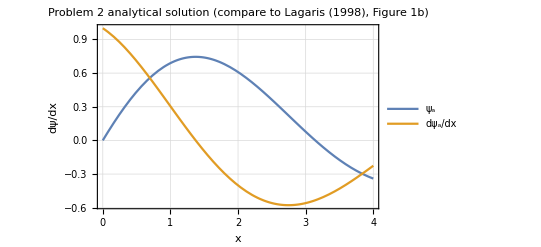

```mathematica
Plot[{ψa[x],dψadx[x]},{x,0,4},AxesLabel->{"x","dψ/dx"},PlotLegends->{"ψ_a","dψ_a/dx"},PlotLabel->"Problem 2 analytical solution (compare to Lagaris (1998), Figure 1b)",Frame->True,GridLines->Automatic]
```